```mathematica
1.;3^100
```

515377520732011331036461129765621272702107522001

```mathematica
2.;3^1000
```

1322070819480806636890455259752144365965422032752148167664920368226828597346704899540778313850608061963909777696872582355950954582100618911865342725257953674027620225198320803878014774228964841274390400117588618041128947815623094438061566173054086674490506178125480344405547054397038895817465368254916136220830268563778582290228416398307887896918556404084898937609373242171846359938695516765018940588109060426089671438864102814350385648747165832010614366132173102768902855220001

```mathematica
3.;N[%]
```

1.32207081948081×10^477

```mathematica
4.;pi=N[π,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

```mathematica
5.;E^((Sqrt[163]pi)/3)
```

640320.00000000060486373504901603947174181881853947577148576036659181946522182582869425363408158226464775899925470001727925679647867303997506923198495665261269396826561338913713441824901972334433096

```mathematica
Answer:小数点后有很多零;
```

```mathematica
6.;StringPosition[StringDrop[ToString[N[Pi,1000]],2],"999999"]
```

{{762,767}}

```mathematica
7.;Sin[13π]
```

0

```mathematica
Log[2.1]
```

0.741937

```mathematica
E^(Sqrt[-1]π)
```

-1

```mathematica
8.;cosPiBy5=Cos[π/5]
```

1/4 (1+√5)

```mathematica
closedForm=(1+Sqrt[5])/4

cosPiBy5==closedForm//FullSimplify
```

1/4 (1+√5)

True

```mathematica
9.;FactorInteger[70612139395722186]
```

{{2,1},{3,2},{43,5},{26684839,1}}

```mathematica
10.;Times@@Apply[Power,{{2,1},{3,2},{43,5},{26684839,1}},1]
```

70612139395722186

```mathematica
11.;(x^2+2 x+1)^20
```

(1+2 x+x^2)^20

```mathematica
Expand[%]
```

1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40

```mathematica
Factor[%]
```

(1+x)^40

```mathematica
12.;(x^2+2 x+1)^20
```

(1+2 x+x^2)^20

```mathematica
Expand[(1+2 x+x^2)^20]
```

1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40

```mathematica
Factor[1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40]
```

(1+x)^40

```mathematica
13.;TrigReduce[Sin[x] Cos[y]-Cos[x] Sin[y]]
```

Sin[x-y]

```mathematica
TrigExpand[%]
```

Cos[y] Sin[x]-Cos[x] Sin[y]

```mathematica
Answer:它们是互相的逆运算;
```

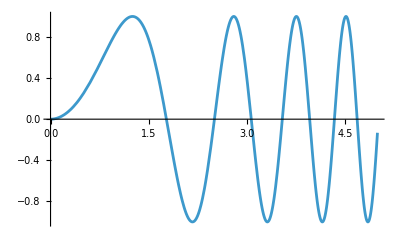

```mathematica
14.;Plot[Sin[x^2],{x,0,5}]
```

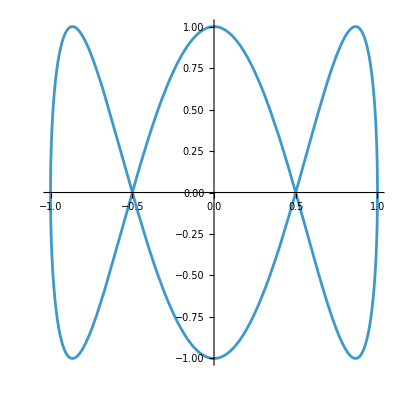

```mathematica
15.;ParametricPlot[{Cos[x],Sin[3 x]},{x,0,2 π}]
```

```mathematica
Answer:这是一个三叶型曲线;
```

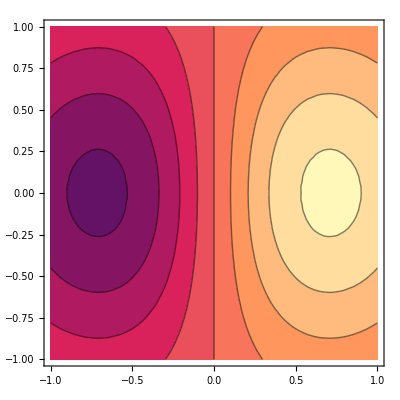

```mathematica
16.;ContourPlot[x E^(-x^2-y^2),{x,-1,1},{y,-1,1}]
```

```mathematica
DensityPlot[x E^(-x^2-y^2),{x,-1,1},{y,-1,1}]
```

-Graphics-

```mathematica
17;∫x/(x^3-1) ⅆx
```

ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

```mathematica
D[(ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]), x]
```

-1/(3 (1-x))-(1+2 x)/(6 (1+x+x^2))+2/(3 (1+1/3 (1+2 x)^2))

```mathematica
Simplify[%]
```

x/(-1+x^3)

```mathematica
18;∫_0^∞ ((Sin^2)[x] (Cos^3)[x])/x ⅆx
```

∫_0^∞ (Cos^3[x] Sin^2[x])/x ⅆx

```mathematica
f[x_]=Sin[x]^2 Cos[x]^3//TrigReduce
analytic=1/16 (2 π/2+π/2-π/2);
N[analytic,20]
numeric1=NIntegrate[(Sin[x]^2 Cos[x]^3)/x,{x,0,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},WorkingPrecision->20,MaxRecursion->20]
numeric2=NIntegrate[(Sin[x]^2 Cos[x]^3)/x,{x,0,∞},Method->{"LevinRule"},WorkingPrecision->20,MaxRecursion->20]

Print["解析值 π/16 = ",N[analytic,20]];
Print["数值结果（DoubleExponential） = ",numeric1];
Print["数值结果（LevinRule） = ",numeric2];
Print["差值（DoubleExponential） = ",Abs[numeric1-N[analytic,20]]];
Print["差值（LevinRule） = ",Abs[numeric2-N[analytic,20]]];
```

1/16 (2 Cos[x]-Cos[3 x]-Cos[5 x])

0.1963495408493620774

```mathematica
19.;∫_0^1 Sin[Sin[x]]ⅆx
```

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,1}]
```

0.430606

```mathematica
20.;s=Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
a x^2+b x+c==0/.s
```

{c+(b (-b-√(b^2-4 a c)))/(2 a)+((-b-√(b^2-4 a c))^2)/(4 a)==0,c+(b (-b+√(b^2-4 a c)))/(2 a)+((-b+√(b^2-4 a c))^2)/(4 a)==0}

```mathematica
Simplify[%]
```

{True,True}

```mathematica
21.;Solve[x^3+x+1==0,x]
```

{{x→},{x→},{x→}}

```mathematica
N[%]
```

{{x→-0.682328},{x→0.341164-1.16154 ⅈ},{x→0.341164+1.16154 ⅈ}}

```mathematica
Answer:My answer satisfy the requirement;
```

```mathematica
22.;mat={{3.5,7.2},{-2.4,6.4}}
```

{{3.5,7.2},{-2.4,6.4}}

```mathematica
Inverse[mat]
Eigenvalues[mat]
```

{{0.16129,-0.181452},{0.0604839,0.0882056}}

{4.95+3.89583 ⅈ,4.95-3.89583 ⅈ}

```mathematica
23.;
mat={{a,b,c},{d,e,f},{g,h,f}}
```

{{a,b,c},{d,e,f},{g,h,f}}

```mathematica
Inverse[mat]
```

{{(e f-f h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(-b f+c h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(-c e+b f)/(-b d f+a e f-c e g+b f g+c d h-a f h)},{(-d f+f g)/(-b d f+a e f-c e g+b f g+c d h-a f h),(a f-c g)/(-b d f+a e f-c e g+b f g+c d h-a f h),(c d-a f)/(-b d f+a e f-c e g+b f g+c d h-a f h)},{(-e g+d h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(b g-a h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(-b d+a e)/(-b d f+a e f-c e g+b f g+c d h-a f h)}}

```mathematica
minv=%
```

{{(e f-f h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(-b f+c h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(-c e+b f)/(-b d f+a e f-c e g+b f g+c d h-a f h)},{(-d f+f g)/(-b d f+a e f-c e g+b f g+c d h-a f h),(a f-c g)/(-b d f+a e f-c e g+b f g+c d h-a f h),(c d-a f)/(-b d f+a e f-c e g+b f g+c d h-a f h)},{(-e g+d h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(b g-a h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(-b d+a e)/(-b d f+a e f-c e g+b f g+c d h-a f h)}}

```mathematica
minv.mat
```

{{((-c e+b f) g)/(-b d f+a e f-c e g+b f g+c d h-a f h)+(d (-b f+c h))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(a (e f-f h))/(-b d f+a e f-c e g+b f g+c d h-a f h),((-c e+b f) h)/(-b d f+a e f-c e g+b f g+c d h-a f h)+(e (-b f+c h))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(b (e f-f h))/(-b d f+a e f-c e g+b f g+c d h-a f h),(f (-c e+b f))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(f (-b f+c h))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(c (e f-f h))/(-b d f+a e f-c e g+b f g+c d h-a f h)},{((c d-a f) g)/(-b d f+a e f-c e g+b f g+c d h-a f h)+(d (a f-c g))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(a (-d f+f g))/(-b d f+a e f-c e g+b f g+c d h-a f h),(e (a f-c g))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(b (-d f+f g))/(-b d f+a e f-c e g+b f g+c d h-a f h)+((c d-a f) h)/(-b d f+a e f-c e g+b f g+c d h-a f h),(f (c d-a f))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(f (a f-c g))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(c (-d f+f g))/(-b d f+a e f-c e g+b f g+c d h-a f h)},{((-b d+a e) g)/(-b d f+a e f-c e g+b f g+c d h-a f h)+(d (b g-a h))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(a (-e g+d h))/(-b d f+a e f-c e g+b f g+c d h-a f h),((-b d+a e) h)/(-b d f+a e f-c e g+b f g+c d h-a f h)+(e (b g-a h))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(b (-e g+d h))/(-b d f+a e f-c e g+b f g+c d h-a f h),((-b d+a e) f)/(-b d f+a e f-c e g+b f g+c d h-a f h)+(f (b g-a h))/(-b d f+a e f-c e g+b f g+c d h-a f h)+(c (-e g+d h))/(-b d f+a e f-c e g+b f g+c d h-a f h)}}

```mathematica
Simplify[%]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
24;rand=Table[RandomReal[1,{3,3}]]
```

{{0.127776,0.277487,0.490566},{0.596675,0.446468,0.888254},{0.60003,0.373059,0.686754}}

```mathematica
rand[[2,2]]=x
```

x

```mathematica
inv=Inverse[rand]
```

{{(-0.331371+0.686754 x)/(0.101045-0.206603 x),-0.00755539/(0.101045-0.206603 x),(0.246479-0.490566 x)/(0.101045-0.206603 x)},{0.12321/(0.101045-0.206603 x),-0.206603/(0.101045-0.206603 x),0.179211/(0.101045-0.206603 x)},{(0.222595-0.60003 x)/(0.101045-0.206603 x),0.118832/(0.101045-0.206603 x),(-0.16557+0.127776 x)/(0.101045-0.206603 x)}}

```mathematica
inv/.x->1
```

{{-3.36671,0.0715756,2.31235},{-1.16722,1.95725,-1.69774},{3.57562,-1.12575,0.358031}}

```mathematica
25.;is=Table[i!,{i,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
26.;Log[is]
```

{0,Log[2],Log[6],Log[24],Log[120],Log[720],Log[5040],Log[40320],Log[362880],Log[3628800]}

```mathematica
data=N[%]
```

{0.,0.693147,1.79176,3.17805,4.78749,6.57925,8.52516,10.6046,12.8018,15.1044}

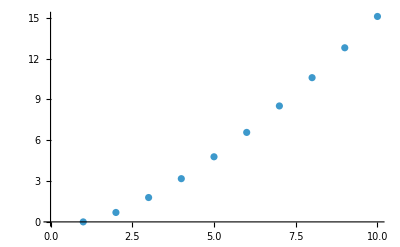

```mathematica
27;p1=ListPlot[data]
```

```mathematica
28.;data=Table[{i,N[Log[i!]]},{i,1,10}]
```

{{1,0.},{2,0.693147},{3,1.79176},{4,3.17805},{5,4.78749},{6,6.57925},{7,8.52516},{8,10.6046},{9,12.8018},{10,15.1044}}

```mathematica
fit=Fit[data,{1,x,x^2,x^3},x]
```

-0.445615+0.229907 x+0.192215 x^2-0.00599207 x^3

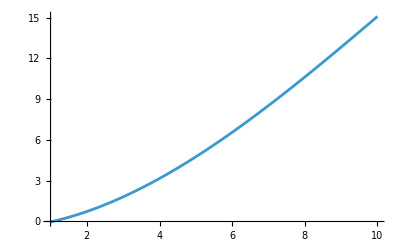

```mathematica
p2=Plot[fit,{x,1,10},PlotRange->All]
```

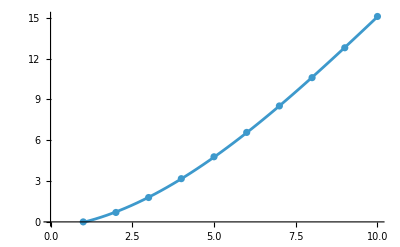

```mathematica
Show[p1,p2]
```

```mathematica
29.;ani2D=Animate[ParametricPlot[{t Cos[s],t Sin[s]},{s,0,2 π},PlotRange->{{-8,8},{-8,8}}],{t,1,6},AnimationRunning->False]
```

```mathematica
ani3D=Animate[Plot3D[Sin[Sqrt[(x-t)^2+y^2]]/Sqrt[(x-t)^2+y^2+0.1],{x,-5,5},{y,-5,5},PlotRange->{-1.2,1.2}],{t,-3,3},AnimationRunning->False]
```

```mathematica
{ani2D,ani3D}
```

{,}

```mathematica
30.;Image@Array[Mod[#+#2,2]&,{64,64}]
```

-Graphics-